```mathematica
SetDirectory[NotebookDirectory[]];
<<"rheology general.wl";
```

## general rheology

```mathematica
rheologyPlots[RHEfolders]
```

## n*

```mathematica
files = FileNames["*.txt", folder]
```

{UDMA\16-10-07\dfs udma 16w 5050 tegdma.txt,UDMA\16-10-07\dfs udma 16w 7525 tegdma.txt,UDMA\16-10-07\dfs udma 16w 8020 tegdma.txt,UDMA\16-10-07\dfs udma 16w 8515 tegdma.txt,UDMA\16-10-07\dfs udma 16w 9010 tegdma.txt,UDMA\16-10-07\dfs udma 16w 9505 tegdma.txt}

```mathematica
parseFiles[folder][[1]]
```

<|{5050}→UDMA\16-10-07\dfs udma 16w 5050 tegdma.txt,{7525}→UDMA\16-10-07\dfs udma 16w 7525 tegdma.txt,{8020}→UDMA\16-10-07\dfs udma 16w 8020 tegdma.txt,{8515}→UDMA\16-10-07\dfs udma 16w 8515 tegdma.txt,{9010}→UDMA\16-10-07\dfs udma 16w 9010 tegdma.txt,{9505}→UDMA\16-10-07\dfs udma 16w 9505 tegdma.txt|>

```mathematica
Grid@Import[files[[1]], "tsv"][[3;;-2, {1, 6}]]
```

0.01 | 0.53201
0.01468 | 0.44751
0.02154 | 1.07332
0.03162 | 0.34872
0.04642 | 0.52158
0.06813 | 0.37107
0.1 | 0.42598
0.14678 | 0.42591
0.21544 | 0.37098
0.31623 | 0.36352
0.46416 | 0.37366
0.68129 | 0.35455
1. | 0.33107
1.4678 | 0.32325
2.15444 | 0.29939
3.16228 | 0.28058
4.64159 | 0.25668
6.81292 | 0.23341
10. | 0.21205
14.678 | 0.20463
21.5444 | 0.19315
31.6228 | 0.37326
46.4159 | 0.16653

50 | 0.53201 | 0.19315
75 | 19.6014 | 1.15168
80 | 65.5432 | 1.90646
85 | 226.529 | 6.11048
90 | 362.732 | 10.0763
95 | 468.385 | 19.0502

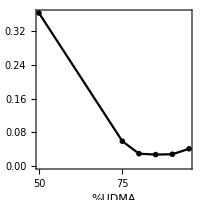

```mathematica
eta = Flatten[{Floor[#/100], Import[parseFiles[folder][[1]][{#}], "tsv"][[{3,23},6]]},1]&/@parseFiles[folder][[2,1]];
Grid[eta]
ListPlot[{#[[1]], #[[3]]/#[[2]]}&/@eta, PlotRange->All, Joined->True , PlotMarkers->●, FrameLabel->{"%UDMA", "η∞"}, ImageSize->200, PlotStyle->Black]
```

```mathematica
{#[[1]], #[[3]]/#[[2]]}&/@eta
```

{{50,0.701603},{75,0.0486195},{80,0.0245107},{85,0.0242853},{90,0.0254837},{95,0.0380443}}